## Optimal control of harmonic oscillator (rest-to-rest transition) Problem 7.4

```mathematica
Clear["Global`*"];
eqs={x''[t]+x[t]==-λ[t],λ''[t]+λ[t]==0};  (* alternatively, four 1st-order eqs *)
init={x[0]==x'[0]==x'[τ]==0,x[τ]==1};
{xs,λs}=DSolveValue[{eqs,init},{x[t],λ[t]},t]//FullSimplify;
Es=1/2(xs^2+D[xs,t]^2)//Simplify;
Js=Integrate[λs^2,{t,0,τ}]//Simplify;
```

```mathematica
TraditionalForm[{xs,λs,Es,Js}]
```

{(2 (t cos(t) (sin(τ)+τ cos(τ))-sin(t) (-t τ sin(τ)+sin(τ)+τ cos(τ))))/(2 τ^2+cos(2 τ)-1),(4 (τ sin(t) cos(τ)+sin(τ) (sin(t)-τ cos(t))))/(2 τ^2+cos(2 τ)-1),(2 ((t τ sin(t) cos(τ)-sin(τ) ((τ-t) sin(t)+t τ cos(t)))^2+(t cos(t) (sin(τ)+τ cos(τ))-sin(t) (-t τ sin(τ)+sin(τ)+τ cos(τ)))^2))/((2 τ^2+cos(2 τ)-1)^2),(4 (τ+sin(τ) cos(τ)))/(2 τ^2+cos(2 τ)-1)}

```mathematica
xdots=D[xs,t]//FullSimplify;TraditionalForm[xdots]
```

(2 sin(τ) ((τ-t) sin(t)+t τ cos(t))-2 t τ sin(t) cos(τ))/(2 τ^2+cos(2 τ)-1)

```mathematica
{xs,xdots,Es}/.t->τ//Simplify
```

{1,0,1/2}

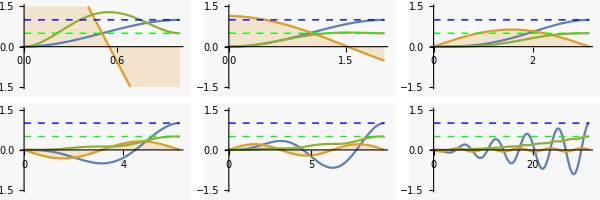

```mathematica
Plotit[τ0_]:=Plot[{xs/.τ->τ0,-λs/.τ->τ0,Es/.τ->τ0,0.5,1},{t,0,τ0},PlotRange->{-1.5,1.5},Filling->{2->Axis},PlotStyle->{,,,Directive[Green,Dashed,Thin],Directive[Blue,Dashed,Thin]}];
p0=Plotit[1];p1=Plotit[2];
p2=Plotit[π];p3=Plotit[2π];
p4=Plotit[3π];
p5=Plotit[10π];
GraphicsGrid[{{p0,p1,p2},{p3,p4,p5}},ImageSize->{600,200}]
```

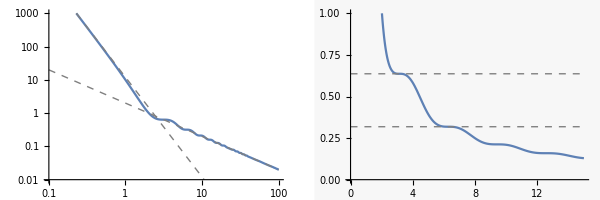

```mathematica
Jlogplot=LogLogPlot[{Js,12/τ^3,2/τ},{τ,0.1,100},PlotStyle->{,Directive[Gray,Dashed,Thin],Directive[Gray,Dashed,Thin]},
PlotRange->{0.01,1000}];
Jlinplot=Plot[{Js,2/π,1/π},{τ,0,15},PlotRange->{0,1},PlotStyle->{,Directive[Gray,Dashed,Thin],Directive[Gray,Dashed,Thin]}];
GraphicsRow[{Jlogplot,Jlinplot},ImageSize->{600,200}]
```

```mathematica
Series[Js, {τ, 0, 1}]
```

12/τ^3-12/(5 τ)+(64 τ)/175+O[τ]^2

```mathematica
Series[2 τ^2+Cos[2 τ]-1,{τ, 0, 8}]
```

(2 τ^4)/3-(4 τ^6)/45+(2 τ^8)/315+O[τ]^9

```mathematica
Dj=D[Js,τ]//Simplify
```

-(16 τ^2 Sin[τ]^2)/((-1+2 τ^2+Cos[2 τ])^2)

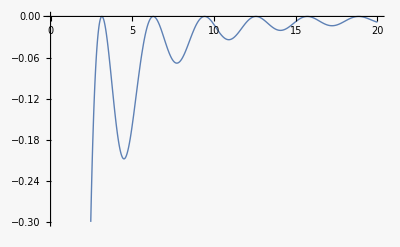

```mathematica
Plot[Dj,{τ,0,20},PlotRange->{-0.3,0}]
```

```mathematica
Solve[Dj==0,τ]
```

{{τ→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{τ→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

```mathematica
Dj/.τ->3π
```

0

```mathematica
Simplify[Js/.τ->n π, Assumptions->n∈Integers]
```

2/(n π)